# Hill Equation Turing Analysis

```mathematica
Solve[10+v-u*(1+v)+a==0&&10+u^-1-v*(1+u^-1)+b==0,{u,v}]
```

```mathematica
{{u->(18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)),v->1/2 (-9-a+99/(11+b)+(11 a)/(2 (11+b))+(29 b)/(2 (11+b))+(a b)/(2 (11+b))+b^2/(2 (11+b))-(11 √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b))-(b √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)))},{u->(18+a+b+√(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)),v->1/2 (-9-a+99/(11+b)+(11 a)/(2 (11+b))+(29 b)/(2 (11+b))+(a b)/(2 (11+b))+b^2/(2 (11+b))+(11 √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b))+(b √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)))}}
```

## Solution 1 (2):

```mathematica
u1=(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b))
v1=1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))
```

(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b))

1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))

```mathematica
Simplify[1+v1-u1-u1*v1+a]
```

0

```mathematica
Simplify[1+u1^-1-v1-u1^-1*v1+b]
```

0

```mathematica
(* wrong code
f[u_,v_]:={1+v-u*(1+v)+a,1+u^-1-v*(1+u^-1)+b} 
point={(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

(*Compute the Jacobian matrix*)
jacobian=JacobianMatrix[f[u,v],{u,v}]/. {u->point[[1]],v->point[[2]]};
simplifiedJacobian=Simplify[jacobian];
MatrixForm[simplifiedJacobian]
*)
```

```mathematica
(*Correct One*)
f[u_,v_]:={1+v-u*(1+v)+a,1+u^-1-v*(1+u^-1)+b}
point={u1,v1}
jacobian=D[f[u,v],{{u,v}}]/. {u->point[[1]],v->point[[2]]};
simplifiedJacobian=Simplify[jacobian];
MatrixForm[simplifiedJacobian]
```

{(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

(1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b))) | 1-(a+b+√(a^2+(4+b)^2+a (8+6 b)))/(2 (2+b))
((2+b)^2 (-4-a+b+√(a^2+(4+b)^2+a (8+6 b))))/((a+b+√(a^2+(4+b)^2+a (8+6 b)))^2) | -1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b))))

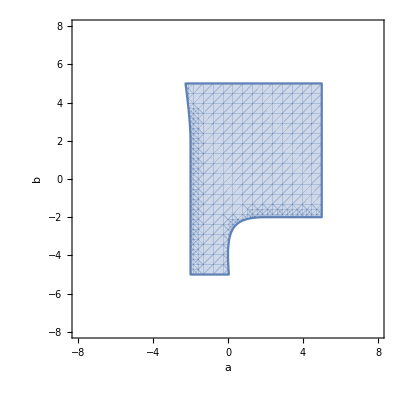

```mathematica
(*Condition 1&&2*)
RegionPlot[1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b)))+(-1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b))))<0&&1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b)))*(-1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b))))-(1-(a+b+√(a^2+(4+b)^2+a (8+6 b)))/(2 (2+b)))*((2+b)^2 (-4-a+b+√(a^2+(4+b)^2+a (8+6 b))))/((a+b+√(a^2+(4+b)^2+a (8+6 b)))^2)>0,{a,-5,5},{b,-5,5},FrameLabel->{"a","b"},LabelStyle->Directive[Black,Medium],PlotRange->{{-8,8},{-8,8}}]
```

```mathematica
a=0.5
b=0.4
```

0.5

0.4

2

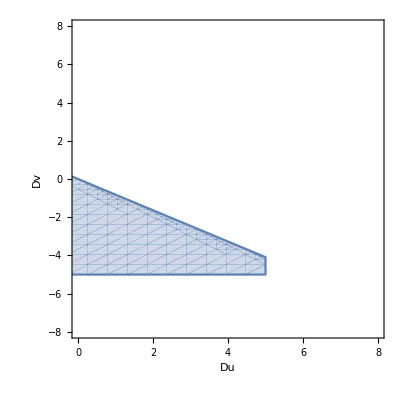

```mathematica
(*Condition 3*)
plot1 =RegionPlot[Du(-1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b))))+Dv(1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b))))>0,{Du,-5,5},{Dv,-5,5},FrameLabel->{"Du","Dv"},LabelStyle->Directive[Black,Medium],PlotRange->{{0,8},{-8,8}}]
```

```mathematica
det=1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b)))*(-1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b))))-(1-(a+b+√(a^2+(4+b)^2+a (8+6 b)))/(2 (2+b)))*((2+b)^2 (-4-a+b+√(a^2+(4+b)^2+a (8+6 b))))/((a+b+√(a^2+(4+b)^2+a (8+6 b)))^2)
```

-(9 (-4+2 √10) (1+1/6 (-2-2 √10)))/(2+2 √10)^2+1/4 (-4-2 √10) (-1-6/(2+2 √10))

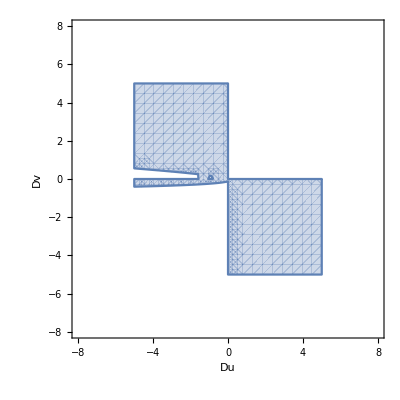

```mathematica
(*Condition 4*)
plot2 =RegionPlot[1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b)))/Du+-1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b)))/Dv>4*det/Du*Dv,{Du,-5,5},{Dv,-5,5},FrameLabel->{"Du","Dv"},LabelStyle->Directive[Black,Medium],PlotRange->{{-8,8},{-8,8}}]
```

## Solution 2 (1):

```mathematica
u2=(18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b))
v2=1/2 (-9-a+99/(11+b)+(11 a)/(2 (11+b))+(29 b)/(2 (11+b))+(a b)/(2 (11+b))+b^2/(2 (11+b))-(11 √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b))-(b √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)))
```

(18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b))

1/2 (-9-a+99/(11+b)+(11 a)/(2 (11+b))+(29 b)/(2 (11+b))+(a b)/(2 (11+b))+b^2/(2 (11+b))-(11 √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b))-(b √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)))

```mathematica
(*Test Solution
Simplify[10+v2-u2-u2*v2+a]
Simplify[10+u2^-1-v2-u2^-1*v2+b]
```

Solution Test

0

0

```mathematica
f[u_,v_]:={10+v-u*(1+v)+a,10+u^-1-v*(1+u^-1)+b}
point={u2,v2}
jacobian=D[f[u,v],{{u,v}}]/. {u->point[[1]],v->point[[2]]};
simplifiedJacobian=Simplify[jacobian];
MatrixForm[simplifiedJacobian]
```

{(18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)),1/2 (-9-a+99/(11+b)+(11 a)/(2 (11+b))+(29 b)/(2 (11+b))+(a b)/(2 (11+b))+b^2/(2 (11+b))-(11 √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b))-(b √(808+80 a+a^2+80 b+6 a b+b^2))/(2 (11+b)))}

(1/4 (-4+a-b+√(808+80 a+a^2+80 b+6 a b+b^2)) | (4-a+b+√(808+80 a+a^2+80 b+6 a b+b^2))/(22+2 b)
-((11+b)^2 (4+a-b+√(808+80 a+a^2+80 b+6 a b+b^2)))/((18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))^2) | -1-(2 (11+b))/(18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2)))

```mathematica
fu2=1/4 (-4+a-b+√(808+80 a+a^2+80 b+6 a b+b^2))
fv2=(4-a+b+√(808+80 a+a^2+80 b+6 a b+b^2))/(22+2 b)
gu2=-((11+b)^2 (4+a-b+√(808+80 a+a^2+80 b+6 a b+b^2)))/((18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))^2)
gv2=-1-(2 (11+b))/(18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))
```

1/4 (-4+a-b+√(808+80 a+a^2+80 b+6 a b+b^2))

(4-a+b+√(808+80 a+a^2+80 b+6 a b+b^2))/(22+2 b)

-((11+b)^2 (4+a-b+√(808+80 a+a^2+80 b+6 a b+b^2)))/((18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))^2)

-1-(2 (11+b))/(18+a+b-√(808+80 a+a^2+80 b+6 a b+b^2))

```mathematica
(*condition1&&2*)
RegionPlot[fu2+gv2<0&&fu2*gv2-fv2*gu2>0,{a,-5,5},{b,-5,5},FrameLabel->{"a","b"},LabelStyle->Directive[Black,Medium],PlotRange->{{0,8},{0,8}}]
```

-Graphics-